# Quantum Cellular Automata

Ruhi Shah

Jonathan Gorard and Tuseeta Banerjee

## Abstract

Everyone has different ideas about what a Quantum Cellular Automaton (QCA) should do. In my opinion, a QCA takes in a quantum state and evolves it using quantum operations that are dependent on its neighbours. This is analogous to the classical CA where classical states (0 or 1) are evolved using classical operations dependent on their neighbours. We define three types of QCA models that could be used to explore. We also show several applications to physics by slightly modifying the QCA model. The first model is based on the quantum teleportation protocol, the second is blha blha and the third is a modification of the second blahblah. Applications in physics include showing the evolution of a quantum state (includes simulating a CNOT gate), showing a coupled two-state system, showing precession of a two state system in a magnetic field, and showing a simple (NN) Heisenberg spin chain. Further applications to physics can be derived from this, and each phenomenon closely explored.

Shout out to Jonathan Gorard for making the Quantum Computing package, that made my life much easier.

```mathematica
Get[FileNameJoin[{NotebookDirectory[],"QuantumComputing.m"}]]
```

## QCA Teleport Model

This model starts with a list of two state systems (qubits).

```mathematica
Subscript[α, 1]|0>+Subscript[β, 1]|1>,Subscript[α, 2]|0>+Subscript[β, 2]|1>,...
```

```mathematica
initialState[n_Integer]:= Join[Table[QuantumFiniteDimensionalState[{{1,0}}],(n-1)/2],{QuantumFiniteDimensionalState[{{0,1}}]},Table[QuantumFiniteDimensionalState[{{1,0}}],(n-1)/2]]
states = initialState[3];
```

The nearest neighbour of a given qubit is “teleported” to the next state using the quantum teleportation protocol. First, a Φ^+ bell state is introduced.

```mathematica
generateEntangledState[]:= QuantumFiniteDimensionalState[{"PhiPlus"}]
entangledpair = generateEntangledState[];
```

The Φ^+ state is then combined with the nearest neighbour qubit, creating a quantum system with 3 qubits. Periodic boundary conditions are applied.

```mathematica
entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[states⟦j+1⟧["StateVector"]],Normal[pair["StateVector"]]}]]/;j≠Length[states]

entangledThreeState[pair_,states_,j_Integer]:=
QuantumFiniteDimensionalState[fixStupidity[{Normal[states⟦1⟧["StateVector"]],Normal[pair["StateVector"]]}]]/;j===Length[states]
```

The nearest neighbour qubit and one of the entangled qubits in the system is put through a CNOT gate, effectively entangling the two. Then the nearest neighbour qubit is put through a Hadamard gate to ensure both exist in the same basis. Then both (nearest neighbour and one of the entangled) are measured using any arbitrary measurement, here I used measurement in σ^xbasis.

```mathematica
entangledMeasurement = QuantumMeasurement["Observable"-> "SigmaX"]

chooseTeleportationOperation[pair_, states_, j_Integer]:=
Flatten[{QuantumEvaluate[{1}-> entangledMeasurement,
QuantumEvaluate[{1}-> operatorHadamard,QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]],
QuantumEvaluate[{2}-> entangledMeasurement, QuantumEvaluate[{1,2}-> operatorCNOT,entangledThreeState[pair,states,j]]]}]
```

QuantumMeasurement[…]

Depending on the measurement obtained above, the nearest neighbour qubit is teleported by transforming the third entangled qubit, allowing us to perform further operations on it later. Also, based on the measurement an operation is chosen for the j^th qubit. There are four possible outcomes: 00, 01, 10, 11. A list of operators is defined. One of the operators is then applied based on the measurement applied.

```mathematica
operators = {operatorHadamard,operatorPauliX,operatorPauliY,operatorPauliZ};
```

```mathematica
applyControlOperation[pair_,states_,j_Integer,operators_]:=
Module[{answer=chooseTeleportationOperation[pair,states,j]},
Which[
answer==={-1,-1},
QuantumEvaluate[{1}-> operators⟦1⟧,states⟦j⟧],
answer==={-1,1},
QuantumEvaluate[{1}-> operators⟦2⟧,states⟦j⟧],
answer==={1,-1},
QuantumEvaluate[{1}-> operators⟦3⟧,states⟦j⟧],
answer==={1,1},
QuantumEvaluate[{1}-> operators⟦4⟧,states⟦j⟧]]]
```

A new qubit is created.

```mathematica
createNewQubit[j_Integer,states_,pair_,operators_]:= 
QuantumFiniteDimensionalState[fixStupidity[{Normal[applyControlOperation[pair,states,j,operators]["StateVector"]]}]]
```

The function is mapped across the entire list of qubits, and a new state is created. The state is then evolved several times, depending on the number of steps (n). This gives a list of states very much like a CA.

```mathematica
nextState[pair_,states_,operators_]:= createNewQubit[#,states,pair,operators]&/@Range[Length[states]]
allStates[pair_,states_,operators_,n_Integer]:= NestList[nextState[pair,#,operators]&,states,n]
```

The result is then turned into standard vectors, that can be manipulated for data analysis.

```mathematica
separateStates[states_]:= Map[Normal[#["StateVector"]]&, states]
separateAllStates[states_]:= separateStates[#]&/@states
```

The number of times a state occurs is counted, and a bar graph produced, this is done for 10,000 steps to ensure there is no anomalies. With the given list of operators, it is expected the number different states is 16. There are 16 degrees of freedom.

```mathematica
countEachState[states_]:= Counts[Flatten[separateAllStates[states],1]]
showCountEachState[states_]:= BarChart[Sort[countEachState[states]], ChartLabels->Automatic,AxesLabel->Automatic, BarOrigin->Left, ImageSize->Large]
```

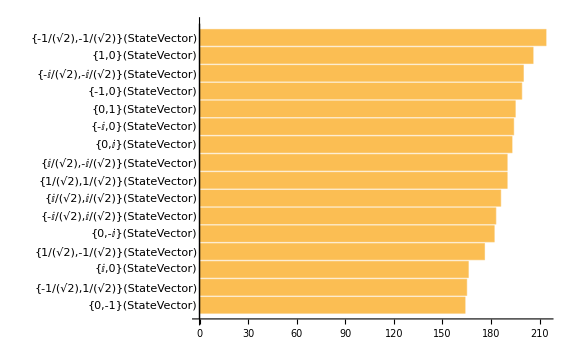

```mathematica
showCountEachState[separateAllStates[allStates[generateEntangledState[],states,operators,1000]]]
```

As expected, there are 16 different states, occurring approximately equally as likely in every large evaluation.

Until now, the QCA looks nothing like a QCA. To visualize the QCA, I represented each complex number as a colour, and each qubit is shown as two separate colours.

```mathematica
colourQubit[qubit_]:= {getColour[qubit⟦1⟧],getColour[qubit⟦2⟧]}
```

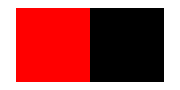
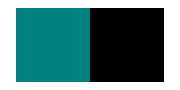
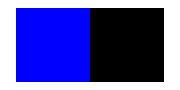
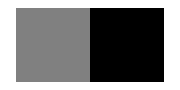
<|-Graphics-→{1,0},-Graphics-→{-1,0},-Graphics-→{ⅈ,0},-Graphics-→{-ⅈ,0}|>

```mathematica
Association[showQubit[{1,0}]-> {1,0},showQubit[{-1,0}]-> {-1,0},showQubit[{I,0}]-> {I,0},showQubit[{-I,0}]-> {-I,0}]
```

Roll over the states to see their vector.

```mathematica
Dynamic[MouseAnnotation[]]
```

```mathematica
colourState[state_]:=Map[colourQubit,state]
colourAll[allstates_]:=Map[colourState, allstates]
showQubit[qubit_]:= Annotation[Rotate[ArrayPlot[{colourQubit[qubit]},Frame -> False,PlotRangePadding->None, ImageSize->Small],3Pi/2], qubit, "Mouse"]
showState[state_]:=Map[showQubit,state]
showAll[allState_]:= GraphicsGrid[Map[showState,allState],ItemAspectRatio->2]
```

Finally, a QuantumCellularAutomataTeleport function can be written, combining everything from before.

```mathematica
QuantumCellularAutomataTeleport[operators_,steps_Integer]:= showAll[separateAllStates[allStates[generateEntangledState[],initialState[steps],operators,steps]]]
```

```mathematica
QuantumCellularAutomataTeleport[operators,50]
```

-Graphics-

```mathematica
Dynamic[MouseAnnotation[]]
```

The result is random, as one would expect. Not sure what to make of it. Here’s another model.

## QCA Poop Model

Another model for the QCA includes evolving an entire state together instead of separate qubits individually. This would be analogous to having some sort of spin chain system. A state of N qubits is taken. I will let N = 3.

```mathematica
states = QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}];
```

The way this model would work is by applying a composition of operations applied on a qubit and its neighbour. There are N qubits and k is the number of operators.

```mathematica
∑_(j=1)^N Subscript[u^k, j] Subscript[u^k, j+1] Subscript[u^(k-1), j] Subscript[u^(k-1), j+1]... Subscript[u^1, j] Subscript[u^1, j+1]
```

```mathematica
oneoperation[j_,n_,states_,matrices_]:= QuantumEvaluate[{j}-> matrices⟦n⟧,QuantumEvaluate[{j+1}-> matrices⟦n⟧,states]] /;n==1
oneoperation[j_,n_,states_,matrices_]:=QuantumEvaluate[{j}->matrices⟦n⟧,QuantumEvaluate[{j+1}->matrices⟦n⟧,oneoperation[j,n-1,states,matrices]]]/;n>1
oneOperationLast[j_,n_,states_,matrices_]:= QuantumEvaluate[{j}-> matrices⟦n⟧,QuantumEvaluate[{1}-> matrices⟦n⟧,states]] /;n==1
oneOperationLast[j_,n_,states_,matrices_]:=QuantumEvaluate[{j}->matrices⟦n⟧,QuantumEvaluate[{1}->matrices⟦n⟧,oneOperationLast[j,n-1,states,matrices]]]/;n>1

nextQubitQCA2[matrices_,j_Integer,states_]:= Normalize[N[Total[Normal[oneoperation[j,Length[matrices],states,matrices]["StateVector"]]&/@Range[Length[matrices]]]]]/;
j≠ Log[2,Length[Normal[states["StateVector"]]]]
nextQubitQCA2[matrices_,j_Integer,states_]:= Normalize[N[Total[Normal[oneOperationLast[j,Length[matrices],states,matrices]["StateVector"]]&/@Range[Length[matrices]]]]]/;
j===Log[2,Length[Normal[states["StateVector"]]]]
```

```mathematica
nextStateQCA2[matrices_,states_]:= QuantumFiniteDimensionalState[fixStupidity[{Total[nextQubitQCA2[matrices,#,states]&/@Range[Log[2,Length[Normal[states["StateVector"]]]]]]}]]
```

```mathematica
evolutionQCA2[matrices_, initialstate_,steps_]:= NestList[nextStateQCA2[matrices,#]&,initialstate,steps]
```

And finally,

```mathematica
QuantumCellularAutomataPoop[matrices_,initialstate_,steps_]:= Rotate[ArrayPlot[colourNQubit[Normal[#["StateVector"]]]&/@evolutionQCA2[matrices,initialstate,steps]],Pi/2]
```

Applying CNOT, Hadamard, and a π/4 rotation about the Z axis can theoretically produce all types of quantum operations.

```mathematica
QuantumCellularAutomataPoop[{operatorCNOT,operatorHadamard,operatorRotate},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],200]
```

-Graphics-

This produces periodic or dying behaviour for all operators applied regardless of initial conditions. The norm squared (probability) of being in a given state can be plotted against time for a series of QCA.

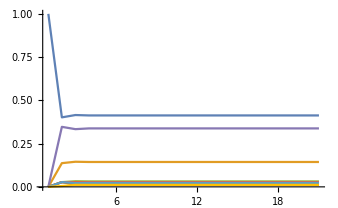

```mathematica
plotNorms[separateStates[evolutionQCA2[{operatorCNOT,operatorHadamard,operatorRotate},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],20]]]
```

The first row contains different combinations of the three logic gates : Hadamard, CNOT, and Rotation Z by Pi/4. The second contains only the logic gates. The third contains two random operators, and a sqrtCNOT gate. The last row contains PauliX, PauliY, and PauliZ.

-Graphics-

The sqrtCNOT gate is one that produces varying probabilities of being in a given state.

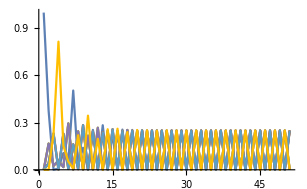

```mathematica
plotNorms[separateStates[evolutionQCA2[{operatorSqrtNOT},QuantumFiniteDimensionalState[{{1,0},{1,0},{1,0}}],50]]]
```

## Applications to Physics

### Evolution of a Two State System

The first thing I wanted to explore is the evolution of a two state system. I took a two level system Hamiltonian, and created an operator that would time evolve it. I introduced the qubit I wanted to evolve.

```mathematica
onequbit = QuantumFiniteDimensionalState[{{1,0}}];
```

I then introduced the Hamiltonian, hbar , the coupling constant t, and epsilon.

```mathematica
$hbar = 1;
$epsilon = 1;
$t = 1;
```

```mathematica
matrixHamiltonian = {{$epsilon,$t},{$t,-$epsilon}};
```

I then defined the time evolution operator.

```mathematica
operatorTime[t_, hamiltonian_] := QuantumMatrixOperation[N[Cos[hamiltonian*t/$hbar], 10] - I*N[Sin[hamiltonian*t/$hbar], 10]]
```

Then I showed the evolution of a qubit for one time step, then mapped that over the entire time step, then displayed the evolution.

```mathematica
qubitEvolve[t_,operator_,initialqubit_,hamiltonian_]:= QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t,hamiltonian],initialqubit]["StateVector"]]}]]
qubitEvolution[operator_,initialqubit_,hamiltonian_]:= qubitEvolve[#,operator,initialqubit,hamiltonian]&/@Range[0,4*Pi,0.5]
showQubitEvolution[operator_,initialqubit_,hamiltonian_]:= GraphicsGrid[{showState[separateStates[qubitEvolution[operator,initialqubit,hamiltonian]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolution[operatorTime,onequbit, matrixHamiltonian]
```

One can see the state evolving back and forth. I then changed epsilon followed by the coupling constant t to see the change in frequence of the evolution.

```mathematica
$epsilon = 2;
matrixHamiltonian = {{$epsilon,$t},{$t,-$epsilon}};
```

```mathematica
showQubitEvolution[operatorTime,onequbit, matrixHamiltonian]
```

-Graphics-

```mathematica
$t = 0.5;
matrixHamiltonian = {{$epsilon,$t},{$t,-$epsilon}};
```

```mathematica
showQubitEvolution[operatorTime,onequbit, matrixHamiltonian]
```

-Graphics-

As expected, increasing epsilon quickens the state evolution and decreasing t slows the evolution.

### Precession of a Two State System in a Magnetic Field

I now try to show the precession of a two state system in a magnetic field. The constant I need is the frequency ω. This for a time independent magnetic field.

```mathematica
omega = 1;
```

The time evolution operator is dependent on the frequency omega.

```mathematica
operatorPrecession[t_] := QuantumMatrixOperation[{{N[Cos[omega*t],10]+ I*N[Sin[omega*t]],0},{N[Cos[omega*t],10]- I*N[Sin[omega*t]],0}}]
```

The evolution is slightly modified by removing the Hamiltonian.

```mathematica
qubitEvolveP[t_,operator_,initialqubit_]:=QuantumFiniteDimensionalState[fixStupidity[{Normal[QuantumEvaluate[{1}-> operator[t],initialqubit]["StateVector"]]}]]
qubitEvolutionP[operator_,initialqubit_]:=qubitEvolveP[#,operator,initialqubit]&/@Range[0,25,0.5]
showQubitEvolutionP[operator_,initialqubit_]:= GraphicsGrid[{showState[separateStates[qubitEvolutionP[operator,initialqubit]]]},ItemAspectRatio->2]
```

```mathematica
showQubitEvolutionP[operatorPrecession,onequbit]
```

-Graphics-

#### Heisenberg Spin Chain (NN)

A Heisenberg spin chain consists of N two state systems interacting with each other. The system has the Hamiltonian:

```mathematica
H=∑_(j=1)^N Subscript[σ^x, j] Subscript[σ^x, j+1]+Subscript[σ^y, j] Subscript[σ^y, j+1]+Subscript[σ^z, j] Subscript[σ^z, j+1]
```

A function is written to evaluate σ^x,σ^y, and σ^zfor a given j and initial states.

```mathematica
sigmaX = QuantumMatrixOperation[{{0,1},{1,0}}];
sigmaY= QuantumMatrixOperation[{{0,-I},{I,0}}];
sigmaZ = QuantumMatrixOperation[{{1,0},{0,-1}}];

transformQubit[j_Integer,states_,operator_]:= Normalize[Normal[QuantumEvaluate[{j}-> operator, QuantumEvaluate[{j+1}-> operator, states]]["StateVector"]]]/;j≠Log[2,Length[Normal[states["StateVector"]]]]
transformQubit[j_Integer,states_,operator_]:= Normalize[Normal[QuantumEvaluate[{j}-> operator, QuantumEvaluate[{1}-> operator, states]]["StateVector"]]]/;j===Log[2,Length[Normal[states["StateVector"]]]]
```

The qubit is then evolved according to the time. The evolution is done for all states.

```mathematica
qubitEvolveH[j_Integer, states_]:= Normalize[((transformQubit[j,states,sigmaX])+(transformQubit[j,states,sigmaY])+(transformQubit[j,states,sigmaZ]))]
qubitStateEvolutionH[t_,states_]:= Normalize[N[Exp[-(I*t*Normalize[Total[qubitEvolveH[#,states]&/@Range[Log[2,Length[Normal[states["StateVector"]]]]]]])/$hbar]]]
qubitEvolutionH[states_,timeduration_,timestep_]:= qubitStateEvolutionH[#,states]&/@Range[0,timeduration,timestep]
```

Plotting the norm squared of each of the elements in the state vector over time.

```mathematica
plotNorms[states_]:= ListLinePlot[Transpose@(Map[Norm[#]^2&,states,{2}]),PlotRange->All]
```

I will start with a state of 3 qubits and see how the system evolves.

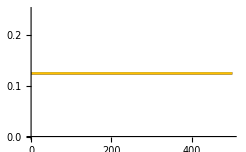

```mathematica
plotNorms[qubitEvolutionH[QuantumFiniteDimensionalState[{{1,0},{0,-1},{1,0}}],10,0.02]]
```

Over time, the system has a probability of being in a given state of exactly 0.125 or 1/8. This means the system is equally likely to be in any of the given states. However, this does not imply that the system isn’t changing. The function colourNQubit colours an N qubit state. If I show the evolution using a QCA differences can be seen.

```mathematica
showHeisenbergEvolution[states_,timeduration_,timestep_]:= Rotate[ArrayPlot[colourNQubit[#]&/@qubitEvolutionH[states,timeduration,timestep]],Pi/2]
```

```mathematica
showHeisenbergEvolution[QuantumFiniteDimensionalState[{{1,1/2},{1/4,I},{0,-1}}],1,0.01]
```

-Graphics-

The parts of the state that change depend on initial conditions. However, the norm squared stays the same which means the probability of being in any given state remains the same. Changing the Hamiltonian might give preference to one state or another, and this can be done depending on the system you are studying.